# Mathematica Tutorial

#### Robert J. Frey, Research Professor http://www.ams.sunysb.edu/~frey/ Stony Brook University, Applied Mathematics and Statistics January 26, 2005

#### Revised 04 Sep 2007 - Updated to V6. Miscellaneous improvements and additions made.

#### Revised 28 Jan 2008 - Minor changes to text.

1 - About This Tutorial

## 1.1 - Mathematica comes bundled with an excellent help system: the Document Browser. This brief tutorial has two rather straightforward objectives. First, I want to get you quickly up to a level where you can begin to use Mathematica's built in help tools productively. In fact, it would be a good idea to have the help browser open as you work through these examples. Second, I want to illustrate some of Mathematica's remarkable capabilities to motivate you to spend the time to learn to use this tool effectively. It's remarkable what can be accomplished in one or two lines of (quite readable) code.

## 1.2 - Probably the best book on Mathematica is the Mathematica Book itself. An electronic copy is bundled with Mathematica. Also very useful for learning how to program in Mathematica is Romans Maeder's Programming in Mathematica.

## 1.3 - I want to emphasize again that this tutorial is neither self-contained nor complete. You need to be stepping through it by executing its code rather than passively reading it. This is an active document and it's a good idea to make small changes as you go along to get an idea of what's happening. Finally, keep the help browser open on your desktop and use it to read deeper into these topics as you work.

## 1.4 - There are also two useful tutorials bundled with Mathematica: An interactive ten minute tour can be found (from the top-line menu) at "Help > Tutorial". A quick tour of Mathematica can be found at "Help > Help Browser > Tour".

2 - Using Mathematica To Compute Interactively

## 2.1 - First, try entering a simple computation: "2 * 3". Pressing <Return> will only put in a new line. You press <Shift-Return> on the keyboard to execute an expression. The first time you submit an expression to the kernel for evaluation there is a lag while the kernel starts up. After this initial delay, things work much faster.

```mathematica
2 * 3
```

6

## 2.2 - Mathematica also follows the usual conventions regarding multiplication: try "2 <Space> 3 <Shift-Return>".

```mathematica
2 3
```

6

```mathematica
3 x+9
```

9+3 x

## 2.3 - Other arithmetic operations work more or less as expected. Note that there is a difference between the integer "2" and the real number (with decimal point) "2.".

### An expression involving only integer frequently results in a rational number.

```mathematica
2/3
```

2/3

```mathematica
2./3
```

0.666667

### Mathematica handles arithmetic involving rational numbers exactly.

```mathematica
(2/3) / (3/10)
```

20/9

### If any of the arguments are real numbers this typically coerces the result to a real number.

```mathematica
(2/3) / (3/10.)
```

2.22222

```mathematica
2.22222-%
```

-2.22222×10^-6

```mathematica
2^3
```

8

```mathematica
2-3.
```

-1.

```mathematica
(-2)3
```

-6

```mathematica
√%
```

ⅈ √6

### Mathematica will handle computations that other systems won't.

```mathematica
2^1000
```

10715086071862673209484250490600018105614048117055336074437503883703510511249361224931983788156958581275946729175531468251871452856923140435984577574698574803934567774824230985421074605062371141877954182153046474983581941267398767559165543946077062914571196477686542167660429831652624386837205668069376

### Integer arguments vs. ...

```mathematica
(2^1000)-(2^999)
```

5357543035931336604742125245300009052807024058527668037218751941851755255624680612465991894078479290637973364587765734125935726428461570217992288787349287401967283887412115492710537302531185570938977091076523237491790970633699383779582771973038531457285598238843271083830214915826312193418602834034688

### Real arguments.

```mathematica
(2.^1000)-(2.^999)
```

5.35754×10^300

### What's the difference here?

```mathematica
2^(-1/3)
```

1/2^(1/3)

```mathematica
2^(-1./3)
```

0.793701

### Euler's Formula!

```mathematica
1+ⅇ^(ⅈ π)
```

0

```mathematica
1+ⅇ^(ⅈ π)
```

0

3 - Simple Symbolic Operations

## 3.1 - Mathematica, as is the case with other programming languages, has symbols. In Mathematica, however, a symbol does not have to have a value to be used in a computation.

### A symbol without a value just returns itself.

```mathematica
x
```

x

### Mathematica tries to do reasonable things with symbolic expressions.

```mathematica
x x
```

x^2

```mathematica
Sin[x]
```

Sin[x]

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

```mathematica
1/(1/x)
```

x

```mathematica
Exp[Log[x]]
```

x

## 3.2 - If you assign a value to a symbol then use the symbol in the expression, Mathematica will repeatedly evaluate the expression until it resolves all of the values it can.

```mathematica
x+y
```

x+y

```mathematica
x=10
```

10

```mathematica
x+y
```

10+y

```mathematica
y=20
```

20

```mathematica
x+y
```

30

```mathematica
Sin[x]
```

Sin[10]

```mathematica
ArcSin[Sin[x]]
```

-10+3 π

```mathematica
ArcSin[Sin[π]]
```

0

### Mathematica's use of exact results is whenever possible is an extension of its symbol manipulation capabilities. This means improved numerical stability. Compare two similar computations, one using a rational argument and another a real argument.

```mathematica
Exp[Log[1/10]]-1/10
```

0

```mathematica
Exp[Log[1/10.]]-1/10.
```

1.38778×10^-17

### You can coerce a result to a real number with the N[ ] function; remember at this point x = 10.

```mathematica
N[Sin[x]]
```

-0.544021

```mathematica
Sin[10.]
```

-0.544021

## 3.3 - Symbolic values are used naturally in many different built-in functions.

### Symbolic differentiaton. The D[f[x], x ] function performs symbolic differentiation of f[ ] with respect to x. It can also be typeset as ∂_x f[x].

```mathematica
D[Sin[z]Cos[z],z]
D[(Sin[z]Cos[z]), z]
```

Cos[z]^2-Sin[z]^2

Cos[z]^2-Sin[z]^2

### Symbolic integration...again note the typeset version

```mathematica
Integrate[√z Log[z],{z,1,2}]
∫_1^2 √z Log[z]ⅆz
```

4/9 (1+√2 (-2+Log[8]))

4/9 (1+√2 (-2+Log[8]))

```mathematica
N[%]
```

0.494377

### While Mathematica will tend to hold exact arguments (e.g., Log[8] above) in a form that will permit simplification in subsequent computation, sometimes you want to coerce a result to real. Note the special variable "%" refers to the most recently returned result.

```mathematica
N[%]
```

### Symbols are evaluated where possible so you must be careful if a function is expecting a symbol argument. Again, recall that we've given x a numeric value, so the following doesn't work.

```mathematica
D[Sin[x]Cos[x],x]
```

General::ivar: 10 is not a valid variable.

∂_10 (Cos[10] Sin[10])

```mathematica
a=2
```

Set::wrsym: Symbol a is Protected.

2

```mathematica
D[Sin[x]Cos[x],x]
```

Cos[x]^2-Sin[x]^2

### Another example of the difference in function results between an integer and real argument.

```mathematica
√Sin[-π/2]
```

ⅈ

```mathematica
√Sin[-π/2.]
```

0.+1. ⅈ

```mathematica
Exp[4 ⅈ]
Exp[4. ⅈ]
```

ⅇ^(4 ⅈ)

-0.653644-0.756802 ⅈ

### The table function is an iterator that generates a list of results. They'll be more about lists later, but for now just think of a simple list being a vector.

```mathematica
Table[z^k,{k,0,10}]
```

{1,z,z^2,z^3,z^4,z^5,z^6,z^7,z^8,z^9,z^10}

```mathematica
FullForm[%]
```

List[1,z,Power[z,2],Power[z,3],Power[z,4],Power[z,5],Power[z,6],Power[z,7],Power[z,8],Power[z,9],Power[z,10]]

```mathematica
Plus[1,2,3]
```

6

### The operation "Plus@@" adds up the elements of a list.

```mathematica
Plus@@{1,2,3,4}
```

10

```mathematica
FullForm[{1,2,3,4}]
```

List[1,2,3,4]

```mathematica
Plus[1,2,3,4]
```

10

### We can combine these elements together to create a rational polynomial.

```mathematica
rf=Plus@@Table[k z^k,{k,0,2}]/Plus@@Table[z^k,{k,0,10}]
```

(z+2 z^2)/(1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)

```mathematica
rf
```

(z+2 z^2)/(1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)

### We can differentiate it once. (Try doing this "by hand"!)

```mathematica
D[rf,z]
```

-((z+2 z^2) (1+2 z+3 z^2+4 z^3+5 z^4+6 z^5+7 z^6+8 z^7+9 z^8+10 z^9))/((1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)^2)+(1+4 z)/(1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)

### Or twice.

```mathematica
D[rf,{z,2}]
```

-(2 (1+4 z) (1+2 z+3 z^2+4 z^3+5 z^4+6 z^5+7 z^6+8 z^7+9 z^8+10 z^9))/((1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)^2)+4/(1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)+(z+2 z^2) ((2 (1+2 z+3 z^2+4 z^3+5 z^4+6 z^5+7 z^6+8 z^7+9 z^8+10 z^9)^2)/((1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)^3)-(2+6 z+12 z^2+20 z^3+30 z^4+42 z^5+56 z^6+72 z^7+90 z^8)/((1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)^2))

### Sometimes it a good idea to ask Mathematica to work a little harder to simplify a result. Again, the "%" argument means the result of the most recent computation. That's the most recent computation executed by the kernel, not necessarily the computation immediately above in the notebook.

```mathematica
Simplify[%]
```

(2 (1-3 z-12 z^2-26 z^3-45 z^4-69 z^5-98 z^6-132 z^7-171 z^8-215 z^9-198 z^10-45 z^11+80 z^12+177 z^13+246 z^14+287 z^15+300 z^16+285 z^17+242 z^18+171 z^19+72 z^20))/(1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)^3

```mathematica
rf
```

(z+2 z^2)/(1+z+z^2+z^3+z^4+z^5+z^6+z^7+z^8+z^9+z^10)

### Symbolic integration can produce a symbolic result.

```mathematica
Integrate[rf,z]
```

RootSum[1+#1+#1^2+#1^3+#1^4+#1^5+#1^6+#1^7+#1^8+#1^9+#1^10&,(Log[z-#1] #1+2 Log[z-#1] #1^2)/(1+2 #1+3 #1^2+4 #1^3+5 #1^4+6 #1^5+7 #1^6+8 #1^7+9 #1^8+10 #1^9)&]

### Symbolic integration can also be definite as well as indefinite

```mathematica
Integrate[rf,{z,-2,2}]
```

-RootSum[1+#1+#1^2+#1^3+#1^4+#1^5+#1^6+#1^7+#1^8+#1^9+#1^10&,(Log[-2-#1] #1+2 Log[-2-#1] #1^2)/(1+2 #1+3 #1^2+4 #1^3+5 #1^4+6 #1^5+7 #1^6+8 #1^7+9 #1^8+10 #1^9)&]+RootSum[1+#1+#1^2+#1^3+#1^4+#1^5+#1^6+#1^7+#1^8+#1^9+#1^10&,(Log[2-#1] #1+2 Log[2-#1] #1^2)/(1+2 #1+3 #1^2+4 #1^3+5 #1^4+6 #1^5+7 #1^6+8 #1^7+9 #1^8+10 #1^9)&]

### Coerce to real.

```mathematica
N[%]
```

0.904573+1.38778×10^-17 ⅈ

### Chop gets rid of "stuff" that is "near" zero.

```mathematica
Chop[%]
```

0.904573

```mathematica
Integrate[rf,{z,-2.,2.}]
```

0.904573

### Numerical integration is also an option. Although this example was able to be solved symbolically, some problems can't be solved in closed form but are perfectly amendable to numerical approximation.

```mathematica
NIntegrate[rf,{z,-2.,2.}]
```

0.904573

### We can plot our rational polynomial.

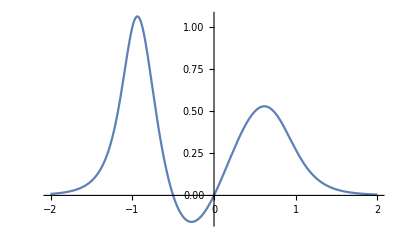

```mathematica
Plot[rf,{z,-2,2}]
```

### Its integral.

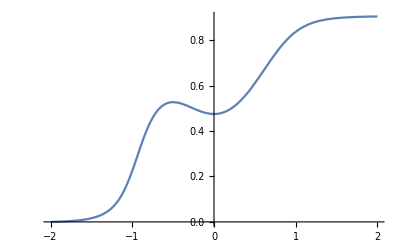

```mathematica
Plot[NIntegrate[rf,{z,-2,i}],{i,-2,2}]
```

### And its derivatives. Certain functions "hold" their arguments, i.e., they pass them in unchanged and then evaluate them later. For a function such as Plot[ ] this makes sense, but sometimes we want to evaluate the argument first and then pass it into the function. With a symbolic derivative of the symbol rf, we want to pass in the actual expression representing the derivative, not the unevaluated D[rf, z]. We do this by forcing an evaluation with Evaluate[ ]. If we hadn't used the Evaluate[ ], then the the D[rf, z] would have been passed into Plot[ ] a value of z would have been substituted in and then an attempt made to evaluate the expression. Not what we want to do. Here are plots of the first and second derivatives.

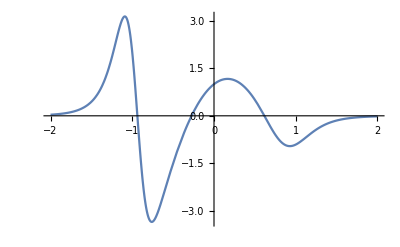

```mathematica
Plot[Evaluate[D[rf, z]],{z,-2,2}]
```

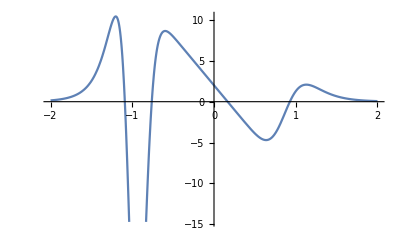

```mathematica
Plot[Evaluate[D[rf, {z,2}]],{z,-2,2}]
```

### Note in the plot above Mathematica has attempted to show what it thought was the "interesting" parts of the plot. We can override this with the appropriate Plot[] option.

```mathematica
PlotRange->All
```

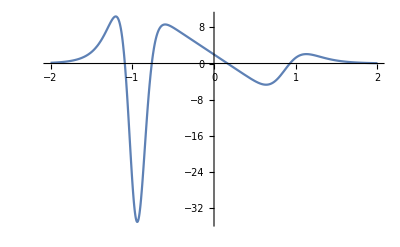

```mathematica
Plot[Evaluate[D[rf, {z,2}]],{z,-2,2},PlotRange->All]
```

4 - Lists

## 4.1 - Vectors

### Here's a simple numeric vector.

```mathematica
v={1,2,3,4,5,6,7,8,9}
```

{1,2,3,4,5,6,7,8,9}

```mathematica
v
```

{1,2,3,4,5,6,7,8,9}

```mathematica
Table[i,{i,1,9}]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
Range[9]
```

{1,2,3,4,5,6,7,8,9}

### Indexing.

```mathematica
v⟦3⟧
```

3

```mathematica
v⟦3⟧
```

3

```mathematica
v[[3]]
```

3

### Mathematica interprets this as squaring each element of the vector and not as multiplying the vector times itself.

```mathematica
v^2
```

{1,4,9,16,25,36,49,64,81}

```mathematica
v.v
```

285

### Most "scalar" functions are applied this way, elementwise.

```mathematica
Sin[v]
```

{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6],Sin[7],Sin[8],Sin[9]}

```mathematica
N[%]
```

{0.841471,0.909297,0.14112,-0.756802,-0.958924,-0.279415,0.656987,0.989358,0.412118}

### Conforming lists work as one might expect.

```mathematica
w=v^2;
v+w
```

{2,6,12,20,30,42,56,72,90}

```mathematica
w-v
```

{0,2,6,12,20,30,42,56,72}

```mathematica
(3 v+10)+w
```

{14,20,28,38,50,64,80,98,118}

```mathematica
{1,2,3}+20
```

{21,22,23}

```mathematica
{1,2,3}+{20}
```

Thread::tdlen: Objects of unequal length in {1,2,3}+{20} cannot be combined.

{20}+{1,2,3}

## 4.2 - Matrices

### A matrix is a list of lists.

```mathematica
q={{1,2},{3,4}}
```

{{1,2},{3,4}}

### You can display a matrix in a more human readable form.

```mathematica
MatrixForm[q]
```

(1 | 2
3 | 4)

### There are a number of functions for computing arrays. Here we use a "pure function". This is very similar to lambda expressions in LISP.

```mathematica
func=#1-#2&
```

#1-#2&

```mathematica
func[3,8]
```

-5

```mathematica
n=Array[#1-#2&,{5,5}]
```

{{0,-1,-2,-3,-4},{1,0,-1,-2,-3},{2,1,0,-1,-2},{3,2,1,0,-1},{4,3,2,1,0}}

```mathematica
MatrixForm[n]
```

(0 | -1 | -2 | -3 | -4
1 | 0 | -1 | -2 | -3
2 | 1 | 0 | -1 | -2
3 | 2 | 1 | 0 | -1
4 | 3 | 2 | 1 | 0)

### There are functions that are specialized to matrices.

```mathematica
MatrixForm[Transpose[n]]
```

(0 | 1 | 2 | 3 | 4
-1 | 0 | 1 | 2 | 3
-2 | -1 | 0 | 1 | 2
-3 | -2 | -1 | 0 | 1
-4 | -3 | -2 | -1 | 0)

```mathematica
IdentityMatrix[5]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
MatrixForm[Reverse[IdentityMatrix[5]]]
```

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[n.Reverse[IdentityMatrix[5]]]
```

(-4 | -3 | -2 | -1 | 0
-3 | -2 | -1 | 0 | 1
-2 | -1 | 0 | 1 | 2
-1 | 0 | 1 | 2 | 3
0 | 1 | 2 | 3 | 4)

### Again, a scalar operation is interpreted elementwise.

```mathematica
MatrixForm[n^2]
```

(0 | 1 | 4 | 9 | 16
1 | 0 | 1 | 4 | 9
4 | 1 | 0 | 1 | 4
9 | 4 | 1 | 0 | 1
16 | 9 | 4 | 1 | 0)

```mathematica
MatrixForm[Transpose[n].n]
```

(30 | 20 | 10 | 0 | -10
20 | 15 | 10 | 5 | 0
10 | 10 | 10 | 10 | 10
0 | 5 | 10 | 15 | 20
-10 | 0 | 10 | 20 | 30)

### The period "." is used for matrix multiplication. Here's a reasonable notion of squaring a matrix.

```mathematica
MatrixForm[Transpose[n].n]
```

(30 | 20 | 10 | 0 | -10
20 | 15 | 10 | 5 | 0
10 | 10 | 10 | 10 | 10
0 | 5 | 10 | 15 | 20
-10 | 0 | 10 | 20 | 30)

### You can also multiply a matrix and vector.

```mathematica
MatrixForm[n.{0,1,2,3,4}]
```

(-30
-20
-10
0
10)

```mathematica
n.{0,1,2,3,4}
```

{-30,-20,-10,0,10}

### There are lots of linear algebra tools. We can generate a random positive semi-definite matrix by multiplying the transpose of a 100 × 70 random matrix with itself. We can then plot the spectrum of that result with a single line of code. Note that the final 30 eigenvalues are zero as expected.

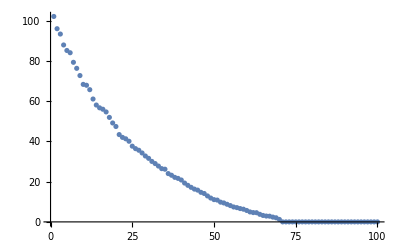

```mathematica
m=(Transpose[#1].#1&)[Table[RandomReal[{-1,1}],{i,1,70},{j,1,100}]];
ListPlot[Chop[Eigenvalues[m]],PlotRange->All]
```

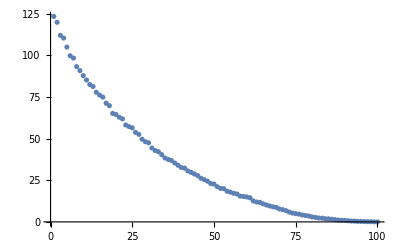

```mathematica
ListPlot[Chop[Eigenvalues[(Transpose[#1].#1&)[Table[RandomReal[{-1,1}],{i,1,100},{j,1,100}]]]],PlotRange->All]
```

## 4.3 - More General Arrays

### Mathematica is very LISP-like in its handling of lists. For example, we might store data on a person's name, address and personal data in a list. The name is itself a list containing the first name and surname. The address is a list containing the street, city, state and zip. The personal data contains the date of birth and height. The date of birth contains the year, month and day. The height contains the number of feet and inches.

```mathematica
a={{"Joe","Smith"},{"1400 Smith St.","Brooklyn","NY",11215},{{1965,03,21},{5,11}}}
```

{{Joe,Smith},{1400 Smith St.,Brooklyn,NY,11215},{{1965,3,21},{5,11}}}

### The person's name is the first element.

```mathematica
a⟦1⟧
```

{Joe,Smith}

### The person's surname is the first element's second part. This can be reached in more than one way.

```mathematica
a⟦1⟧⟦2⟧
```

Smith

```mathematica
a⟦1,2⟧
```

Smith

### The month of birth is the third element's first element's second element.

```mathematica
a⟦3,1,2⟧
```

3

### There are more complex forms of indexing.

```mathematica
a⟦{1,2}⟧
```

{{Joe,Smith},{1400 Smith St.,Brooklyn,NY,11215}}

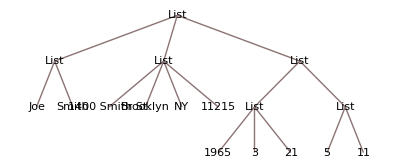

```mathematica
TreeForm[a]
```

```mathematica
FullForm[a]
```

List[List["Joe","Smith"],List["1400 Smith St.","Brooklyn","NY",11215],List[List[1965,3,21],List[5,11]]]

### There are also a number of useful functions.

```mathematica
First[a]
```

{Joe,Smith}

```mathematica
Last[a]
```

{{1965,3,21},{5,11}}

```mathematica
Prepend[a,10]
```

{10,{Joe,Smith},{1400 Smith St.,Brooklyn,NY,11215},{{1965,3,21},{5,11}}}

```mathematica
Append[a,10]
```

{{Joe,Smith},{1400 Smith St.,Brooklyn,NY,11215},{{1965,3,21},{5,11}},10}

```mathematica
Length[a]
```

3

```mathematica
Length[a⟦3,2⟧]
```

2

```mathematica
Length/@a
```

{2,4,2}

```mathematica
TreeForm[a]
```

```mathematica
TreeForm[{{1,2,3},5}]
```

```mathematica
FullForm[{{1,2,3},5}]
```

5. Simple Graphics



```mathematica
Plot[Sin[x],{x,0,2 π}]
```

```mathematica
Table[{x π,Sin[x π]},{x,0,2,0.25}]
```

{{0.,0.},{0.785398,0.707107},{1.5708,1.},{2.35619,0.707107},{3.14159,1.22465×10^-16},{3.92699,-0.707107},{4.71239,-1.},{5.49779,-0.707107},{6.28319,-2.44929×10^-16}}

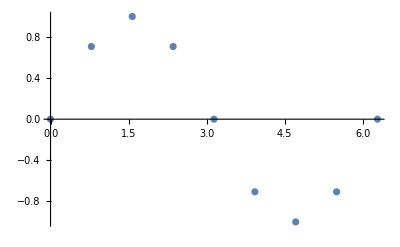

```mathematica
ListPlot[Table[{x π,Sin[x π]},{x,0,2,0.25}]]
```

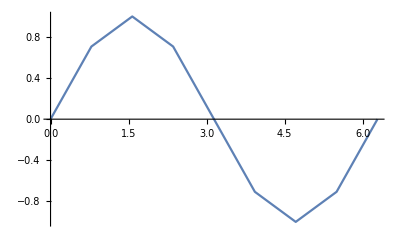

```mathematica
ListPlot[Table[{x π,Sin[x π]},{x,0,2,0.25}],Joined->True]
```

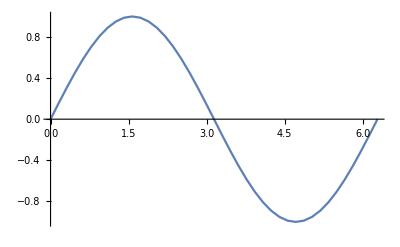

```mathematica
ListPlot[Table[{x π,Sin[x π]},{x,0,2,0.05}],Joined->True]
```

```mathematica
ListPlot[Table[{x π,Sin[x π]},{x,0,2,0.01}]]
```

```mathematica
Plot3D[Sin[x] Cos[y],{x,-π,π},{y,-π,π}]
```

-Graphics3D-

```mathematica
ContourPlot[Sin[x] Cos[y],{x,-π,π},{y,-π,π}]
```

```mathematica
ParametricPlot[{8Sin[θ],3Cos[θ]},{θ,-π,π},AspectRatio->1]
```

```mathematica
ParametricPlot[{Sin[x]/2,(2 Cos[x])/3},{x,-π,π},PlotRange->{{-1,1},{-1,1}},AspectRatio->1]
```

6. Simple Programming

## 6.1 - Sometimes You Don't Need a Program

### There are many instances in which a line or so of Mathematica does the work that would require significant programming effort in other environments. Note that we have assigned a value to the symbol "x" but we want to use it as a pure symbol, so we have to "clear" it.

```mathematica
Remove["Global`*"]
Solve[3 x+10==√2,x]
```

### Here's a list of the first 100 prime numbers.

```mathematica
Table[Prime[i],{i,1,100}]
```

### There are a number of special functions built in that you won't need to code up. Here's a sample of the Bessel function of the first kind.

```mathematica
Plot[BesselJ[3,x],{x,-20,20}]
```

### There's already a Mean[ ] function...

```mathematica
Mean[{10,3,4,11,2,4,5}]
```

### But it's simple enough to cook one up.

```mathematica
(Plus@@#)/Length[#]&[{10,3,4,11,2,4,5}]
```

## 6.2 - Programming Examples

```mathematica
f[x_,y_]:=x^y;
```

### We can now use this function to compute x^y.

```mathematica
f[2,3]
```

### Sometimes we need local variables. Here's an example of a (not very efficient) variance function. The function implicitly assumes the input is a numeric vector. We enclose the function definition in a Module[ ]. The first argument is a list of local variable names. The second argument is a compound statement representing the function body. Note the placement of commas (,) and semi-colons (;). The last statement evaluated is the return value.

```mathematica
var[x_]:=Module[
{m,n},
n=Length[x];
m=(Plus@@x)/n;
(Plus@@((x-m)^2))/(n-1)
];
```

```mathematica
var[{1.,2,3,4}]
```

```mathematica
Variance[{1.,2.,3.,4.}]
```

7. Cool Examples - It's remarkable what you can accomplish in a few lines of code.

## 7.1 - Computations

### The yield to maturity of a bond is that constant interest rate when applied to its cash flows produces a present value equal to its price. For example, a semi-annual bond with a face value of F, coupon of C, term of N years and price P, the yield y solves the following equation

P=∑_(t=1)^(2N-1) C/(1+y/2)^t+(F+C)/(1+y/2)^(2N)

Background: http://en.wikipedia.org/wiki/Bond_valuation

### Consider a new 20 year bond with a $1,000 face value and a coupon rate of 10% compounded semi-annually. The semi-annual coupon is, therefore, $1,000 × 10% / 2 = $50. The bond sold at a discount to its face value for a price of $975. We use FindRoot[ ] to solve this problem. The yield is 10.4%.

Clean up any user defined symbols. "Global" is the default context (i.e., namespace) for user defined symbols and "*" has the usual meaning as in a regular expression.

```mathematica
Remove["Global`*"]
```

Generate a vector of cashflows: the price is a negative cashflow at t = 0, followed by 19 coupon payments, and terminated by the final coupon payment plus the face amount.

```mathematica
cf=Join[{-975},Table[50,{k,1,19}],{1050}]
```

Generate a symbolic vector of discount factors based on the unknow yield y.

```mathematica
df=Table[(1+y/2)^-k,{k,0,20}]
```

The problem is to find the root of the following inner product.

```mathematica
df.cf
```

This is accomplished with

```mathematica
FindRoot[cf.df,{y,0.1}]
```

Note that the solution is returned as a vector of replacement rules.

## 7.2 - Graphics

Source: Oliver Knill, knill@math.harvard.edu. Although I made a few minor changes to the original code, the two excellent examples below can be found at  http://www.math.harvard.edu/computing/math/tutorial/.

### This is the Henon attractor. One of the better known examples of a chaotic map. Note the NestList function in the second line to generate successive recursions.

Background: http://en.wikipedia.org/wiki/Henon_map

```mathematica
T[{x_,y_}]:={0.3 y+1-1.4 x^2,x};
ListPlot[
NestList[T,{0.5,0.3},10^4],
PlotStyle->{PointSize[Small]}
]
```

### Here's a plot of the Mandelbrot set. This example uses a compiled function to speed up its computations: two lines of code!

Background: http://en.wikipedia.org/wiki/Mandelbrot_set

```mathematica
M=Compile[
{x,y},
Block[
{z=x+ⅈ y,k=0},
While[Abs[z]<2&&k<50,z=z^2+x+ⅈ y;++k];
k
]
];
DensityPlot[
50-M[x,y],
{x,-2.3,1.3},{y,-1.4,1.4},
Frame->False,
PlotPoints->100,
Mesh->False,
ColorFunction->(Hue[1-#1]&),
AspectRatio->1/GoldenRatio
]
```